## Ground Product State Tomography

```mathematica
(* N atoms in the instance from Nbar poissonian statistics*)
poisson[Nbar_,N_]:=PDF[PoissonDistribution[Nbar],N];
(*Probability of measuring k atoms among N atoms being at F=1, after rotating by θ*)
(*Blow-away failure rate = ϵ*)
(*This function gives the probability detecting k atoms among N atoms in F=1 state, after microwave pulse area θ has been applied to |0>^N*)
Prob[N_,k_,θ_,ϵ_]:=N!/((N-k)!(k)!) ((1-ϵ)Cos[θ/2]^2)^((N-k))(ϵ Cos[θ/2]^2+Sin[θ/2]^2)^k;

(*Probability of measuring single excitation in W-state*)
ProbW[N_,θ_]:=(N-1)Cos[θ/2]^(2N-4)Sin[θ/2]^4+Cos[θ/2]^(4N)+(N-1)(N-2)Cos[θ/2]^(2N-4)Sin[θ/2]^4-2(N-1)Cos[θ]^(3N-2)Sin[θ/2]^2;
(* This gives Poissonian averaged probability*)
FullProb[Nbar_,k_,θ_,ϵ_]:=Sum[poisson[Nbar,N]Prob[N,k,θ,ϵ],{N,0,3Nbar}];
```

## Data Analysis

Need two batch of analysis to distinguish three cases (1) more than 2 atoms, (2) exactly 1atom and (3) no atom.

```mathematica
SetDirectory[NotebookDirectory[]]
Needs["ErrorBarPlots`"]
```

C:\Users\Xnei\Dropbox\Research\2015\2015-05-28\Dephased W-state Microwave Analysis

```mathematica
Ω=2π*5.89(*kHz*)
t2pi=2π/Ω;
{nd1,errs1}=Import["analysis1normData.m"];
{nd2,errs2}=Import["analysis2normData.m"];
gd1=Import["analysis1generalData.m"];
gd2=Import["analysis1generalData.m"];
(*xs=CutIterLabels[gd1][[2;;-1,1]]*)
xs=10^-3{0.,10.,20.,30.,40.,50.,60.,70.,80.,90.,100.};
xs= xs /t2pi*2π;
(*xs=Mod[xs+π,2π]-π;*)
```

37.008

```mathematica
P2=nd1[[3]];
P1=(1-nd1[[3]])*nd2[[3]];
P0=(1-nd1[[3]])*(1-nd2[[3]]);
P2errs=errs1[[3]];
P1errs=(1-nd1[[3]])errs2[[3]]+errs1[[3]]*nd2[[3]];
P0errs=(1-nd1[[3]])errs2[[3]]+errs1[[3]]*(1-nd2[[3]]);
```

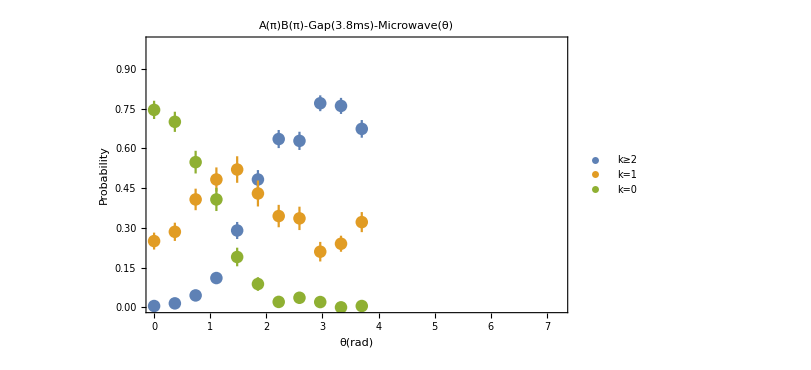

```mathematica
plot2=ErrorListPlot[{Transpose[{Transpose[{xs,P2}],ErrorBar/@P2errs}],Transpose[{Transpose[{xs,P1}],ErrorBar/@P1errs}],Transpose[{Transpose[{xs,P0}],ErrorBar/@P0errs}]},PlotStyle->PointSize[0.015],Frame->True,FrameLabel->{"θ(rad)","Probability"},PlotRange->{{0,2.3π},{0,1}},PlotLegends->{"k≥2","k=1","k=0"},LabelStyle->FontSize->16,ImageSize->600,PlotLabel->Style["A(π)B(π)-Gap(3.8ms)-Microwave(θ)",FontSize->20]]
```

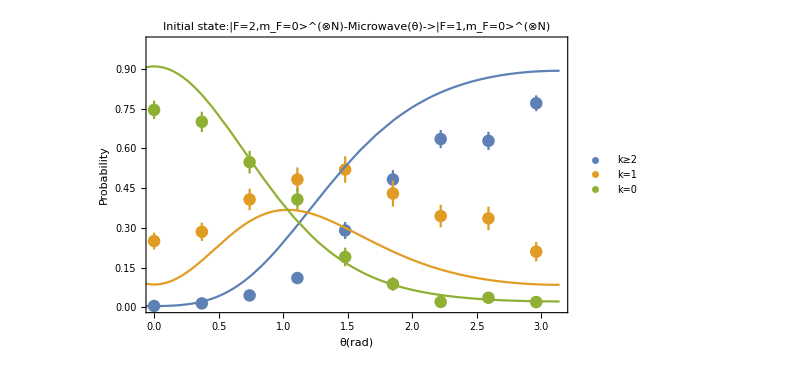

```mathematica
nbar=3.8;
ϵ=2.5 10^-2;
plot3=Show[plot2,Plot[{1-FullProb[nbar,0,θ,ϵ]-FullProb[nbar,1,θ,ϵ],FullProb[nbar,1,θ,ϵ],FullProb[nbar,0,θ,ϵ]},{θ,-π,π}]]
```

```mathematica
Export["20150529_WGapMicrowave.png",plot2]
Export["20150529_WGapMicrowave.pdf",plot2]
```

20150529_WGapMicrowave.png

20150529_WGapMicrowave.pdf

```mathematica
Sum[Prob[10,k,0.2,10^-2],{k,0,10}]
```

1.